```mathematica
Clear["Global`*"]
```

```mathematica
d=1;
U01=4;
U02=0;
a=3;
b=1;
at=a-b;
bt=a+b;
Rsink=1;
Rmax=25;
t0=0;
t1=500;
wmin=1
wmax=5
datapoints =wmax-wmin+1
u1[r_]:=U01 Exp[-((r-a)/b)^n];
u2[r_]:=U02 Exp[-((r-a)/b)^n];
pde = {D[ρ1[r,t],t]==2/r ρ1[r,t] u1'[r]+D[ρ1[r,t],r]u1'[r]+ρ1[r,t] u1''[r]+d 2/r D[ρ1[r,t],r]+d D[ρ1[r,t],r,r]-w12 ρ1[r,t] + w21 ρ2[r,t],
D[ρ2[r,t],t]==2/r ρ2[r,t] u2'[r]+D[ρ2[r,t],r]u2'[r]+ρ2[r,t] u2''[r]+d 2/r D[ρ2[r,t],r]+d D[ρ2[r,t],r,r]-w21 ρ2[r,t] + w12 ρ1[r,t]
};
bc = {
ρ1[Rsink,t]==0,
ρ2[Rsink,t]==0,
ρ1[Rmax,t]==w21/(w12+w21),
ρ2[Rmax,t]==w12/(w12+w21)
};
ic = {
ρ1[r,t0]==w21/(w12+w21)*(1-1/r),
ρ2[r,t0]==w12/(w12+w21)*(1-1/r)
};
```

1

5

5

```mathematica
Densities=Table[0,{k,1,3},{i,1,datapoints+1}];
ReactionRate=Table[0,{k,1,2},{i,1,datapoints+1}];
Densities2=Table[0,{k,1,3},{i,1,datapoints+1}];
ReactionRate2=Table[0,{k,1,2},{i,1,datapoints+1}];
```

```mathematica
For[i=0,i<=datapoints,i++,
n=2^6;
w12=10^(wmin+(wmax-wmin)*i/datapoints);
w21=w12;
sol=NDSolve[{pde,bc,ic},{ρ1,ρ2},{t,t1,t1},{r,Rsink,Rmax},MaxSteps->Infinity,MaxStepFraction->0.002,AccuracyGoal->15,StartingStepSize->0.001,WorkingPrecision->MachinePrecision,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->24000}}];
Print["Done","i=",n,"w12=",N[w12],"w21=",N[w21]];
ρ1eq[r_]=ρ1[r,t1]/.sol;
ρ2eq[r_]=ρ2[r,t1]/.sol;
ρtot[r_]=(ρ1[r,t1]+ρ2[r,t1])/.sol;

Densities[[1,i+1]]=ρ1eq[r];
Densities[[2,i+1]]=ρ2eq[r];
Densities[[3,i+1]]=ρtot[r];
ReactionRate[[1,i+1]]=w12;
ReactionRate[[2,i+1]]=D[ρtot[r],r]/.r->1;

]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

NDSolve::eerr: Warning: scaled local spatial error estimate of 24.824 at t = 500. in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 24000 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

Donei=64w12=10.w21=10.

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::eerr: Warning: scaled local spatial error estimate of 23.8667 at t = 500. in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 24000 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

Donei=64w12=63.0957w21=63.0957

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve :: ibcinc will be suppressed during this calculation.

NDSolve::eerr: Warning: scaled local spatial error estimate of 21.9879 at t = 500. in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 24000 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

General::stop: Further output of NDSolve :: eerr will be suppressed during this calculation.

Donei=64w12=398.107w21=398.107

Donei=64w12=2511.89w21=2511.89

Donei=64w12=15848.9w21=15848.9

Donei=64w12=100000.w21=100000.

```mathematica
Um[r_]:=(U01+U02)/2* Exp[-((r-a)/b)^n]
DebyeLimit = NIntegrate[Exp[Um[r]]/(d*r^2),{r,Rsink,Infinity}]^(-1)
```

0.390772

{94.1887,{x→2.00025}}

General::unfl: Underflow occurred in computation.

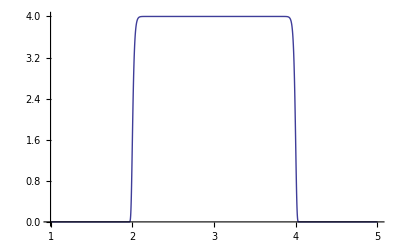

General::unfl: Underflow occurred in computation.

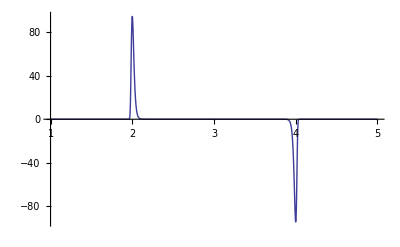

```mathematica
FindMaximum[u1'[x],{x,2}]
Plot[u1[x],{x,1,5},PlotRange->All]
Plot[u1'[x],{x,1,5},PlotRange->All]
```

```mathematica
Export["ww4.pdf",Plot[Densities[[All,1]],{r,1,6}]];
Export["ww6.pdf",Plot[Densities[[All,3]],{r,1,6}]];
Export["ww8.pdf",Plot[Densities[[All,4]],{r,1,6}]];
Export["ww10.pdf",Plot[Densities[[All,5]],{r,1,6}]];
```

```mathematica
resolution=100;
rho1=Table[0,{i,1,resolution},{j,1,datapoints}];
rho2=Table[0,{i,1,resolution},{j,1,datapoints}];
```